```mathematica
Fitness[q_,nu_,qs_]:=If [nu≠Infinity,Exp[(1/nu) Cos[2 Pi q- 2 Pi qs]]/( BesselI[0,1/nu]),1];
```

```mathematica
a = 0.5;
Q =0.25;
μ = 0.2;
qs = 0.5;
 
g[x_,nu_] :=Q a x/μ NIntegrate[ Fitness[qq, nu, qs]/(μ + a x Fitness[qq,nu,qs]),{qq,0,1}]
```

# Coexistence between generalist and specialits.

## Using NDSolve in Mathematica for the von Mises fitness

```mathematica
(* Contains the dynamics of empty resources *)MeanField[com_,other_]:=Module[{NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult},
(* This is the parameter for species*)

NSP =Length[com];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)

initialE= Table[ρE[q][0]==0.1*B/μ,{q,QQ}];
initialO= Table[ρ[sp,q][0]== 0.9B/(μ NSP),{sp,NSP},{q,QQ}]; (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
fO[sp_,q_,t_]:=-μ * ρ[sp,q][t]+ρE[q][t]* aa[[sp]]*fitn[[sp,Round[q/qstep]]]* qstep*Sum[ρ[sp,qq][t],{qq,QQ}];


systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];
systemO=Table[ρ[sp,q]'[t]==fO[sp,q,t],{sp,NSP},{q,QQ}];

Fullsystem=Flatten[{systemE,systemO,initialE,initialO}];

variableE=Table[ρE[q],{q,QQ}];
variableO=Table[ρ[sp,q],{sp,NSP},{q,QQ}];

Fullvariable=Flatten[{variableE,variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
Result0=Evaluate[Table[ρ[sp,q][TMAX/2.],{sp,NSP},{q,QQ}] /.Solution];

(*This one is for the abundance at the end of the simulation*)
Result1=Evaluate[Table[ρ[sp,q][TMAX],{sp,NSP},{q,QQ}] /.Solution];

finalResult= {Flatten[Result0,1],Flatten[Result1,1]}; 
finalResult]
```

```mathematica
(*TRYING TO MAKE THE CODE FASTER BY REMOVING RESOURCE DYNAMCS*)MeanField2[com_,other_]:=Module[{NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult},
(* This is the parameter for species*)

NSP =Length[com];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)

(*initialE= Table[ρE[q][0]==0.1*B/μ,{q,QQ}];*)
initialO= Table[ρ[sp,q][0]== 0.9B/(μ NSP),{sp,NSP},{q,QQ}]; (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
(*fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];*)

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
fO[sp_,q_,t_]:=-μ * ρ[sp,q][t]+(B/μ - Sum[ρ[ssp,q][t],{ssp,NSP}])* aa[[sp]]*fitn[[sp,Round[q/qstep]]]* qstep*Sum[ρ[sp,qq][t],{qq,QQ}];


(*systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];*)
systemO=Table[ρ[sp,q]'[t]==fO[sp,q,t],{sp,NSP},{q,QQ}];

Fullsystem=Flatten[{(*systemE,*)systemO,(*initialE,*)initialO}];

(*variableE=Table[ρE[q],{q,QQ}];*)
variableO=Table[ρ[sp,q],{sp,NSP},{q,QQ}];

Fullvariable=Flatten[{(*variableE,*)variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
Result0=Evaluate[Table[ρ[sp,q][TMAX/2.],{sp,NSP},{q,QQ}] /.Solution];

(*This one is for the abundance at the end of the simulation*)
Result1=Evaluate[Table[ρ[sp,q][TMAX],{sp,NSP},{q,QQ}] /.Solution];

finalResult= {Flatten[Result0,1],Flatten[Result1,1]}; 
finalResult]
```

```mathematica
localdir = "C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim4\\";  qS1 = 0.25; qS2= 0.75; as =0.5;
NU= Flatten[{Subdivide[0.05,2,50],4,8,16}];
pag = 1;
BB =Flatten[{0.002,0.004,0.006,0.008,0.01,0.015, Range[0.02,2,0.2],4,8}];
```

```mathematica
time1= AbsoluteTiming[
Do[
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};
middata= enddata= {};
Do[
com1= {qS1,ν,as};
com2 = {qS2 ,ν, as};
COM = {com1,com2};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,NU}];
Export[localdir<>"2spe_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",middata];
Export[localdir<>"2spe_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",enddata];
,{B,BB}];
]; (* about 11 min*)


time2= AbsoluteTiming[
Do[
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};
middata= enddata= {};
Do[
com1= {qS1,ν,as};
com2 = {qS2 ,ν, as};
com3 = {0. ,ν, as};
com4 = {0.5 ,ν, as};
COM = {com1,com2,com3,com4};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,NU}];
Export[localdir<>"4spe_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",middata];
Export[localdir<>"4spe_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",enddata];
,{B,BB}];
]; 

qS1 = 1./3; qS2 = 2./3; qS3 = 1.;
time3= AbsoluteTiming[
Do[
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000}; 
middata= enddata= {};
Do[
com1= {qS1,ν,as};
com2 = {qS2 ,ν, as};
com3 = {qS3 ,ν, as};
COM = {com1,com2,com3};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,NU}];
Export[localdir<>"3spe_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",middata];
Export[localdir<>"3spe_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",enddata];
,{B,BB}];
];
```

```mathematica
time3
```

{537.076,Null}

### Plotting coexistence as a function of nu and colonization rate

```mathematica
localdir = "C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim4\\";
```

```mathematica
BB =Flatten[{0.002,0.004,0.006,0.008,0.01,0.015, Range[0.02,2,0.2],4,8}];
```

```mathematica
(* equilibrium for the generalist*)
eqg[pag_,B_]:= 1 - μ^2/(B as pag);
```

```mathematica
(*  2 specialists *)
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000}; pag = 1;

R1 = {};
Do[
data = ToExpression@Import[localdir<>"2spe_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

result1 = {};

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Total[subd[[2;;]],2]/NSTEP  μ/B;
AppendTo[result1, {nu,occ}];
,{l,Length[data]}];
AppendTo[R1,result1];
,{B,BB}];

R2 = {};
Do[
data = ToExpression@Import[localdir<>"2spe_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];
result2 = {};
Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Total[subd[[2;;]],2]/NSTEP  μ/B;
AppendTo[result2, {nu,occ}];
,{l,Length[data]}];
AppendTo[R2,result2];
,{B,BB}];
```

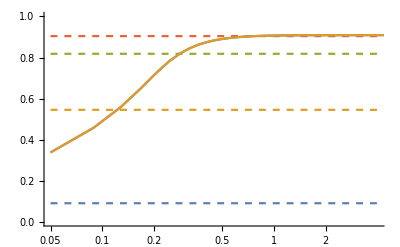

```mathematica
nb =8;
gen =LogLinearPlot[{eqg[0.1,BB[[nb]]],eqg[0.2,BB[[nb]]],eqg[0.5,BB[[nb]]],eqg[0.95,BB[[nb]]]},{x,0.05,4},PlotRange->{{0.05,4},{0,1}}, PlotStyle->Dashed];

spe =ListLogLinearPlot[{R1[[nb]],R2[[nb]]}, Joined->True,PlotRange->{{0.05,4},{0,1}}];

fig1 = Show[gen,spe]
```

```mathematica
(*  3 specialists *)
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000}; pag = 1;

R3 = {};
Do[
data = ToExpression@Import[localdir<>"3spe_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

result3 = {};

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Total[subd[[2;;]],2]/NSTEP  μ/B;
AppendTo[result3, {nu,occ}];
,{l,Length[data]}];
AppendTo[R3,result3];
,{B,BB}];

R4 = {};
Do[
data = ToExpression@Import[localdir<>"3spe_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];
result4 = {};
Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Total[subd[[2;;]],2]/NSTEP  μ/B;
AppendTo[result4, {nu,occ}];
,{l,Length[data]}];
AppendTo[R4,result4];
,{B,BB}];
```

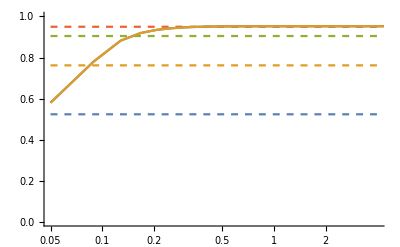

```mathematica
nb = 9;
gen =LogLinearPlot[{eqg[0.1,BB[[nb]]],eqg[0.2,BB[[nb]]],eqg[0.5,BB[[nb]]],eqg[0.95,BB[[nb]]]},{x,0.05,4},PlotRange->{{0.05,4},{0,1}}, PlotStyle->Dashed];

spe =ListLogLinearPlot[{R3[[nb]],R4[[nb]]}, Joined->True,PlotRange->{{0.05,4},{0,1}}];

fig2 = Show[gen,spe]
```

```mathematica
(*  4 specialists *)
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000}; pag = 1;

R5 = {};
Do[
data = ToExpression@Import[localdir<>"4spe_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

result5 = {};

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Total[subd[[2;;]],2]/NSTEP  μ/B;
AppendTo[result5, {nu,occ}];
,{l,Length[data]}];
AppendTo[R5,result5];
,{B,BB}];

R6 = {};
Do[
data = ToExpression@Import[localdir<>"4spe_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];
result6 = {};
Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Total[subd[[2;;]],2]/NSTEP  μ/B;
AppendTo[result6, {nu,occ}];
,{l,Length[data]}];
AppendTo[R6,result6];
,{B,BB}];
```

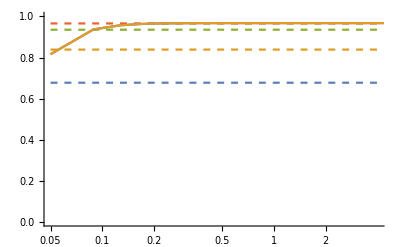

```mathematica
nb = 10;
gen =LogLinearPlot[{eqg[0.1,BB[[nb]]],eqg[0.2,BB[[nb]]],eqg[0.5,BB[[nb]]],eqg[0.95,BB[[nb]]]},{x,0.05,4},PlotRange->{{0.05,4},{0,1}}, PlotStyle->Dashed];

spe =ListLogLinearPlot[{R5[[nb]],R6[[nb]]}, Joined->True,PlotRange->{{0.05,4},{0,1}}];

fig2 = Show[gen,spe]
```

```mathematica
Export[localdir<>"2spe_2gen.jpeg",F3,ImageResolution->100];
Export[localdir<>"3spe_1gen.jpeg",F2,ImageResolution->100];
Export[localdir<>"2spe_1gen.jpeg",F1,ImageResolution->100];
```

#### Finding a criteria for nu, ag and B

```mathematica
nb = 12;
fig = {};
Do[
data = R2[[nb]]; bb = BB[[nb]];
gg[occ_]:= μ^2/(bb as(1 -occ));

newd = Transpose[{data[[All,1]], gg[data[[All,2]]]}];

tempf =ListLogLinearPlot[newd, Joined->True,PlotRange->{{0.05,4},{0,1}}];
AppendTo[fig,tempf];
,{nb,{8,12,18}}];
```

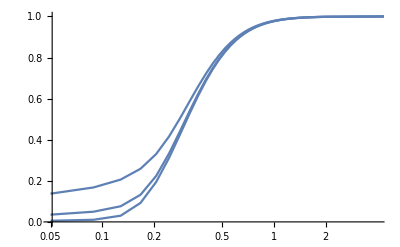

```mathematica
f2 =Show[fig]
```

```mathematica
qS1 =0.25;
qS2 =0.75;
data= {};
Quiet[
Do[

bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

ovff[q_]:= Min[ff[q,ν, qS1],ff[q,ν, qS2]];
ov = NIntegrate[ovff[q],{q,0,1}];
AppendTo[data,{ν,ov}];
,{ν,NU}]
];ovdata = data;
```

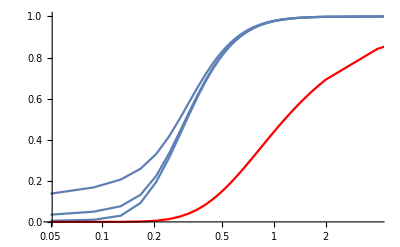

```mathematica
d2 =ListLogLinearPlot[ovdata,Joined->True,PlotStyle->Red];
Show[f2,d2]
```

```mathematica
qS1 =0.25; md = {};
Do[
bs =  BesselI[0,1/ν];
ff[q_,ν_,qs_]:=Exp[ Cos[2 Pi (q-  qs)]/ν]/bs;

AppendTo[md, {ν, ff[0.5,ν, qS1]}];

,{ν, NU}];
```

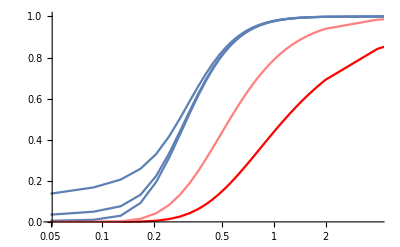

```mathematica
fmd =ListLogLinearPlot[md,Joined->True,PlotStyle->Pink];
Show[f2,d2,fmd]
```